Parameters

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
boxLength=1000;
```

```mathematica
lattIdx=173;
```

```mathematica
importLattice[lattIdx_]:=Module[
{latt,lattComplete},
latt=Import["lattice_v"<>IntegerString[lattIdx,10,3]<>"/lattice/0000.txt","Table"][[;;,1]];

	lattComplete=ConstantArray[0,boxLength];
Do[
lattComplete[[l]]=1;
,{l,latt}];

Return[lattComplete];
];
```

```mathematica
latt=importLattice[lattIdx];
```

Visualize the lattice

```mathematica
visualizeLattice[lattice_,boxLength_,color_,left_,right_]:=Graphics[
Table[
{Blend[{White,color},lattice[[i]]],EdgeForm[Thin],Rectangle[{i,0}]}
,{i,left,right}]
,Background->White];
```

```mathematica
showColumns[latt_,nColumn_,interval_,color_]:=Column[Table[
Show[visualizeLattice[latt,boxLength,color,(i-1)*interval+1,i*interval],ImageSize->800]
,
{i,1,nColumn}
]]
```

```mathematica
Manipulate[
showColumns[importLattice[iLatt],10,100,Blue]
,{iLatt,1,200,1}]
```

Activate hidden

```mathematica
activateHidden[boxLength_,latt_,w_,binary_]:=Module[
{hiddenLatt,idxs,vals,p,act}
,
hiddenLatt=ConstantArray[0,boxLength];
Do[
If[i==1,
idxs={i,i+1};
];
If[i==boxLength,
idxs={i-1,i};
];
If[i≠1&&i≠boxLength,
idxs={i-1,i,i+1};
];

act=0.0;
Do[
act+=latt[[idx]];
,{idx,idxs}];

act*=w;
act=LogisticSigmoid[act];

If[binary
,
If[RandomReal[{0,1}]<act,
hiddenLatt[[i]]=1.0,
hiddenLatt[[i]]=0.0
];
,
hiddenLatt[[i]]=act;
];
,{i,1,boxLength}];

Return[hiddenLatt];
];
```

```mathematica
w=0.0;
```

```mathematica
hiddenLatt=activateHidden[boxLength,latt,w,True];
```

Show both hidden and visible

```mathematica
showColumns[latt_,nColumn_,interval_,color_]:=Column[Table[
Show[visualizeLattice[latt,boxLength,color,(i-1)*interval+1,i*interval],ImageSize->800]
,
{i,1,nColumn}
]]
```

```mathematica
visualizeBoth[lattV_,lattH_,left_,right_]:=Module[
{g}
,
g=Graphics[Join[
Table[
{Blend[{White,Blue},lattV[[i]]],EdgeForm[Thin],Rectangle[{i,0}]}
,{i,left,right}],
Table[
{Blend[{White,Red},lattH[[i]]],EdgeForm[Thin],Rectangle[{i,-1}]}
,{i,left,right}]
]
,Background->White];
Return[g]
];
```

```mathematica
showBoth[lattV_,lattH_,nColumn_,interval_]:=Column[Table[
Show[visualizeBoth[lattV,lattH,(i-1)*interval+1,i*interval],ImageSize->800]
,
{i,1,nColumn}
]]
```

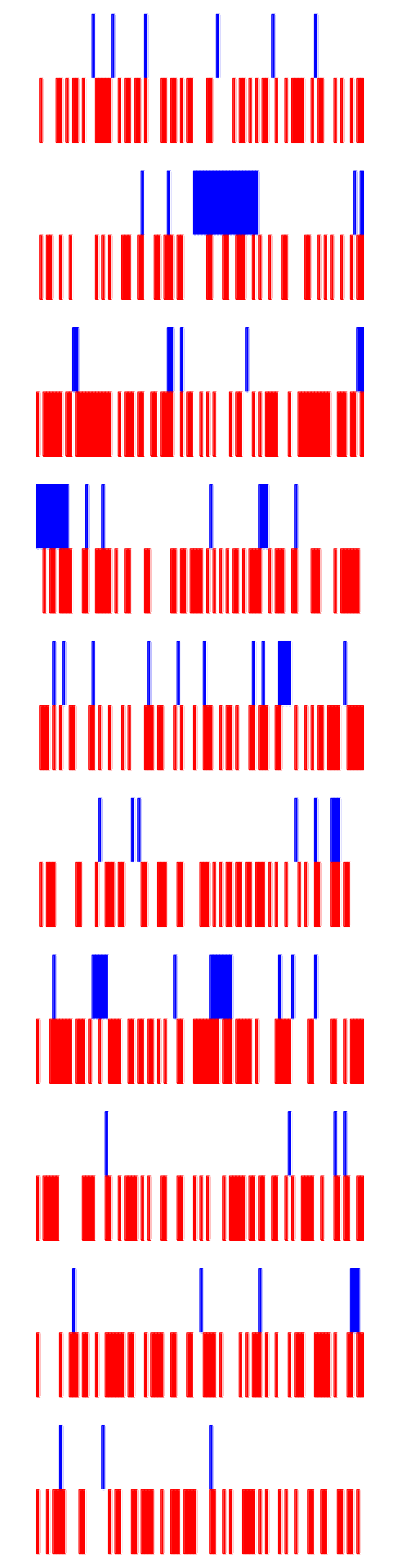

```mathematica
showBoth[latt,hiddenLatt,10,100]
```

Calculate moment

```mathematica
calcMoment[boxLength_,latt_,hiddenLatt_]:=Module[
{mom,p,idxs}
,
mom=0.0;
(* Go through hidden lattice *)
Do[

If[i==1,
idxs={i,i+1};
];
If[i==boxLength,
idxs={i-1,i};
];
If[i≠1&&i≠boxLength,
idxs={i-1,i,i+1};
];

Do[
mom+=hiddenLatt[[i]]*latt[[idx]];
,{idx,idxs}];

,{i,1,boxLength}];

Return[mom];
];
```

```mathematica
nSamples=20;
```

```mathematica
moms={};
Do[
hiddenLatt=activateHidden[boxLength,latt,w,True];
AppendTo[moms,calcMoment[boxLength,latt,hiddenLatt]];
,{iSample,1,nSamples}];
```

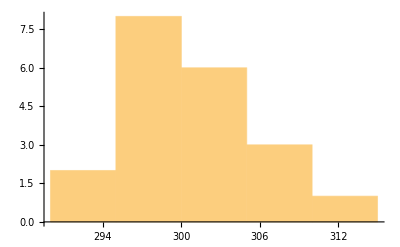

```mathematica
Histogram[moms]
```

Sample the visible

```mathematica
sampleLatt[h_,w_,hiddenLatt_,boxLength_]:=Module[
{latt,act,idxs,p}
,
latt=ConstantArray[0,boxLength];

Do[
act=h;

If[ipos==1,
idxs={ipos,ipos+1}
];
If[ipos==boxLength,
idxs={ipos-1,ipos}
];
If[ipos!=1&&ipos≠boxLength,
idxs={ipos-1,ipos,ipos+1}
];

Do[
act+=w*hiddenLatt[[idx]];
,{idx,idxs}];

act=LogisticSigmoid[act];

(* USE PROBABILITIES! *)
latt[[ipos]]=act;

,{ipos,1,boxLength}];

Return[latt]
];
```

```mathematica
runCD[h_,w_,lattH_,boxLength_,nCD_,returnFinalHidden_]:=Module[
{lattV,lattHS}
,
lattHS=lattH;
Do[
lattV=sampleLatt[h,w,lattHS,boxLength];
If[iCD≠nCD||returnFinalHidden==True,
lattHS=activateHidden[boxLength,lattV,w,False];
];
,{iCD,1,nCD}];

If[returnFinalHidden,
Return[{lattV,lattHS}],
Return[lattV]
];
];
```

### Example

```mathematica
h=-4;
```

```mathematica
w=3.0;
```

```mathematica
hiddenLatt=activateHidden[boxLength,latt,w,True];
```

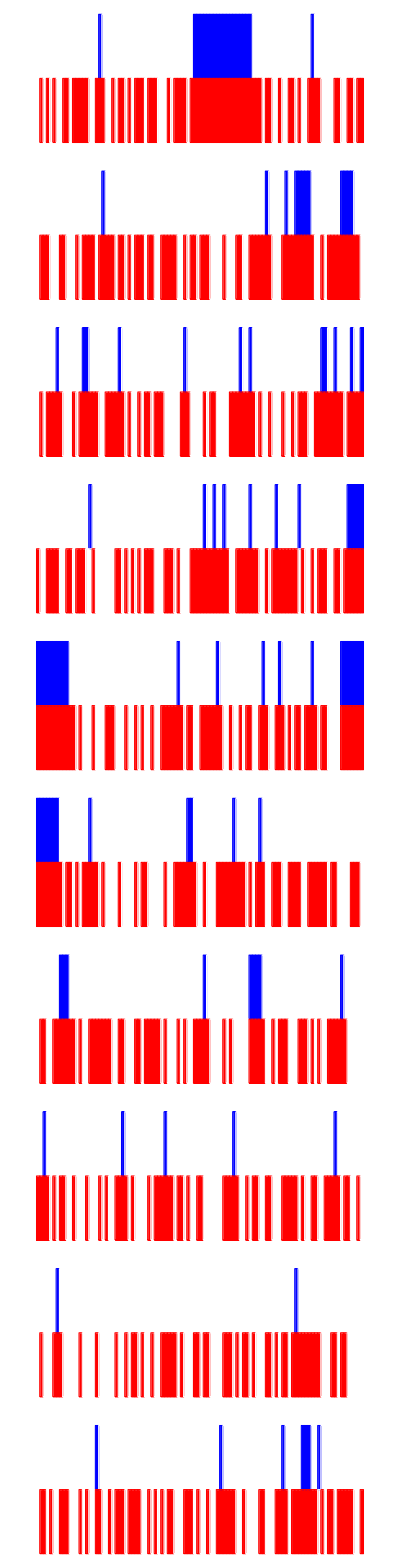

```mathematica
showBoth[latt,hiddenLatt,10,100]
```

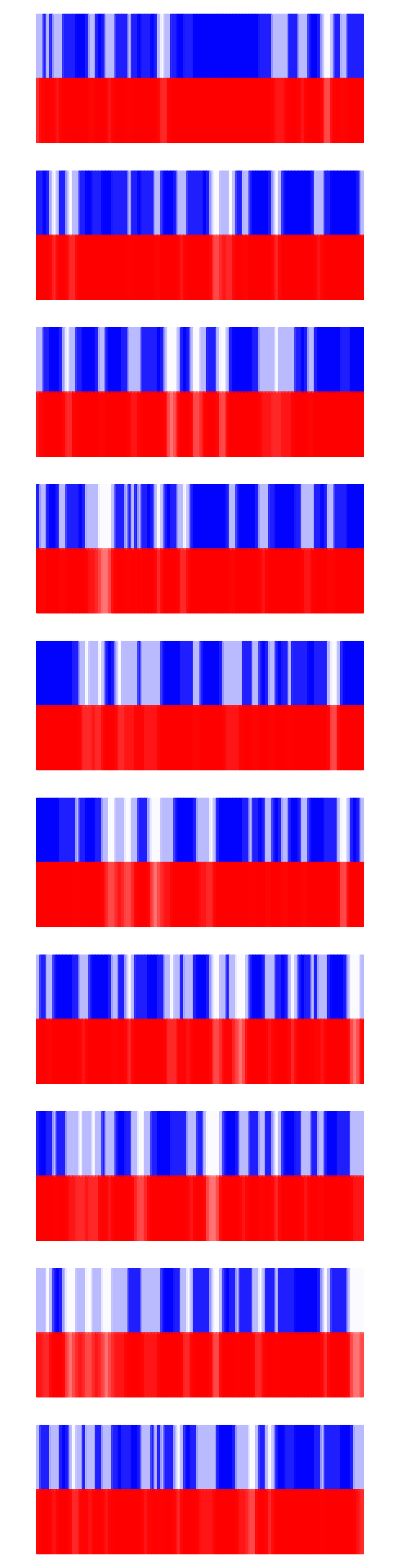

```mathematica
{lattNew,hiddenLattNew}=runCD[h,w,hiddenLatt,boxLength,1,True];
showBoth[lattNew,hiddenLattNew,10,100]
```

```mathematica
calcMoment[boxLength,lattNew,hiddenLattNew]
```

1920.83

## Try BMLA

```mathematica
bmla[wstart_,hstart_,learningRateW_,learningRateh_,noCDsteps_,nSteps_,boxLength_,nBatch_]:=Module[
{wSt,hSt,lattV,lattH,awakeW,awakeWSt,awakeh,awakehSt,asleepW,asleepWSt,asleeph,asleephSt,lattComplete}
,
(* Store *)
wSt={wstart};
hSt={hstart};

awakeWSt={};
asleepWSt={};
awakehSt={};
asleephSt={};

(* Visible and hidden latts *)
lattV=ConstantArray[0,boxLength];
lattH=ConstantArray[0,boxLength];

(* Learn *)
Monitor[

(* No learning steps *)
Do[

awakeW=0.0;
asleepW=0.0;
awakeh=0.0;
asleeph=0.0;

(* Batch *)
Do[

(* Read in data *)
lattV=importLattice[RandomInteger[{101,120}]];

(* Activate hidden -> binary *)
lattH=activateHidden[boxLength,lattV,wSt[[-1]],False];

(* Awake moment *)
awakeW+=calcMoment[boxLength,lattV,lattH];
awakeh+=Total[lattV];

(* CD *)
{lattV,lattH}=runCD[hSt[[-1]],wSt[[-1]],lattH,boxLength,1,True];

(* Asleep moment *)
asleepW+=calcMoment[boxLength,lattV,lattH];
asleeph+=Total[lattV];

,{iBatch,1,nBatch}];

(* Average *)
awakeW/=nBatch;
asleepW/=nBatch;
awakeh/=nBatch;
asleeph/=nBatch;

(* Store *)
AppendTo[awakeWSt,awakeW];
AppendTo[awakehSt,awakeh];
AppendTo[asleepWSt,asleepW];
AppendTo[asleephSt,asleeph];

(* Increment *)
AppendTo[wSt,wSt[[-1]]-learningRateW*(asleepW-awakeW)];
AppendTo[hSt,hSt[[-1]]-learningRateh*(asleeph-awakeh)];

,{iStep,1,nSteps}];

,Row[{
ProgressIndicator[iStep,{1,nSteps}],
ListLinePlot[wSt,ImageSize->400,PlotRange->{{0,nSteps},Automatic}],
ListLinePlot[hSt,ImageSize->400,PlotRange->{{0,nSteps},Automatic}],
ListLinePlot[{awakeWSt,asleepWSt},ImageSize->400,PlotRange->{{0,nSteps},Automatic}],
ListLinePlot[{awakehSt,asleephSt},ImageSize->400,PlotRange->{{0,nSteps},Automatic}]
}]];

Return[{wSt,hSt,awakeWSt,asleepWSt,awakehSt,asleephSt}]
];
```

```mathematica
wstart=1.0;
hstart=-3;
```

```mathematica
learningRateW=0.0001;
learningRateh=0.0001;
```

```mathematica
noCDsteps=10;
```

```mathematica
nSteps=1000;
```

```mathematica
nBatch=100;
```

```mathematica
{wSt,hSt,awakeWSt,asleepWSt,awakehSt,asleephSt}=bmla[wstart,hstart,learningRateW,learningRateh,noCDsteps,nSteps,boxLength,nBatch];
wLearned=wSt[[-1]];
hLearned=hSt[[-1]];
```

$Aborted

```mathematica
wLearned
```

0.645945

```mathematica
hLearned
```

-0.913304

### Viz

```mathematica
wTest=0.6;
hTest=-2.7;
```

```mathematica
showBoth[latt,hiddenLatt,10,100]
```

-Graphics-

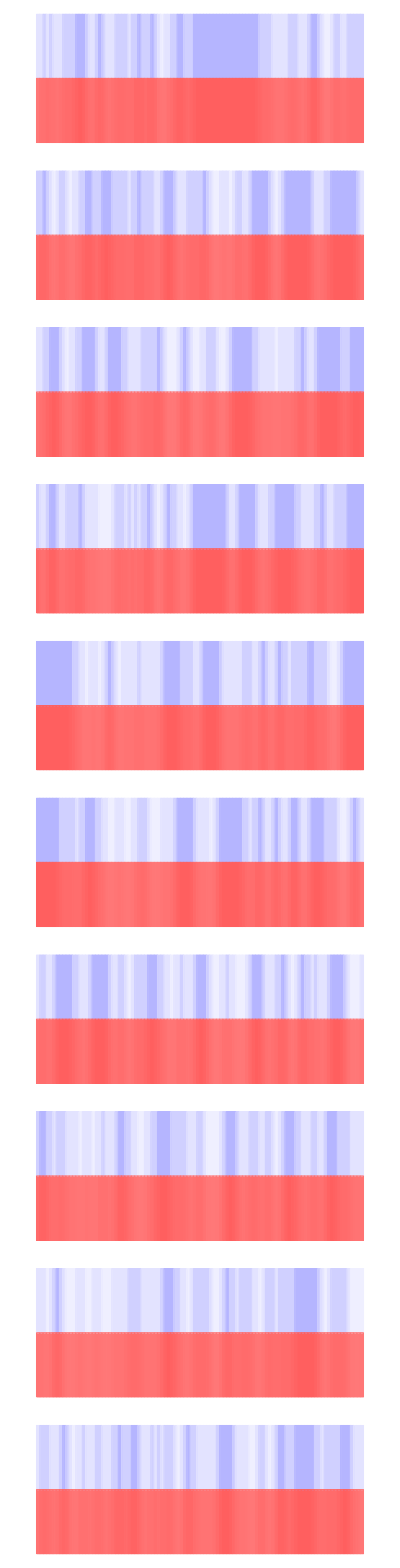

```mathematica
lattNew=sampleLatt[hTest,wTest,hiddenLatt,boxLength];
hiddenLattNew=activateHidden[boxLength,lattNew,wTest,False];
showBoth[lattNew,hiddenLattNew,10,100]
```

```mathematica
calcMoment[boxLength,latt,hiddenLatt]
```

332.

```mathematica
calcMoment[boxLength,lattNew,hiddenLattNew]
```

313.963

```mathematica
Total[latt]
```

113

```mathematica
Total[lattNew]
```

177.541